```mathematica
r[x_]:= x+ r0

r0 = 1/(4 c);
Veff[x_] := 1/(8r[x]^2) -c/r[x] + 2c^2
```

```mathematica
phiminusone[x_]:= Assuming[x>=0&&c>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
pot[x_] := -c k^2Exp[-b*25*r[x]/k^2]/r[x]
Eminustwo = -2c^2;
Es = {Eminustwo};
phis = {phiminusone[x]};
Eminusone = -1/2(D[phis[[1]],x] /. x-> 0)-1/(2 r[0]^2);
AppendTo[Es,Eminusone];
phizero[s_] :=Simplify[( Es[[2]] + 1/(2r[s]^2) +1/2(D[phis[[1]],x] /.x->s))/(-phiminusone[s])]
AppendTo[phis,phizero[x]];

Ezero = 3/(8 r[0]^2)-1/2(D[phis[[2]],x]/. x->0)-1/2( phis[[2]]^2 /. x->0) +SeriesCoefficient[pot[x],{k,Infinity,0}] /. x->0;
phione[s_] := Simplify[(-3/(8 r[s]^2)+1/2(D[phis[[2]],x]/. x->s)+1/2( phis[[2]]^2 /. x->s) -SeriesCoefficient[pot[x],{k,Infinity,0}] + Ezero)/(-phiminusone[s])]
```

```mathematica
Energy[n_]:= Energy[n] = Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,True, Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]+(SeriesCoefficient[pot[x],{k,Infinity,n}]/. x->0)]]
phi[n_]:= phi[n] = Which[n==-1,phiminusone[x],n==0,phizero[x],n==1,phione[x],True,Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]- SeriesCoefficient[pot[x],{k,Infinity,n-1}])/(-phiminusone[x])]]
```

```mathematica
Clear[phi,Energy]
```

```mathematica
Clear[c,k]


Clear[c]
```

```mathematica
c=1/25
```

1/25

```mathematica
Energy[100];
```

$Aborted

```mathematica
k=5
```

5

```mathematica
maxkOrder = 50
perturbationorder = 13
EnergySeries = Expand[Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}],k],b]],b]] + O[b]^(perturbationorder+1)] ;
EnergySeriesplusOne= Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder+1}],k],b]],b]+O[b]^(perturbationorder+1)];
```

50

13

```mathematica
Coefficients = {-2/(k-1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Coefficientstwo = {-2/(k-1)^2};
Do[AppendTo[Coefficientstwo,Collect[Coefficient[EnergySeriesplusOne, b,n],k] ],{n,1,perturbationorder}]
```

```mathematica
(*Table[Length[Coefficients[[n]] /. Sum ->List],{n,1,perturbationorder+1}]*)
Table[Coefficients[[n]] -Coefficientstwo[[n]],{n,1,perturbationorder+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
k =3
```

3

```mathematica
PartialSums = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
PadeNN = Table[PadeApproximant[PartialSums[[n]],{b,0,Floor[n/2]}] ,{n,3,perturbationorder}];
PadeNNplusone = Table[PadeApproximant[PartialSums[[n]],{b,0,{Floor[n/2],Floor[n/2]+1}}] ,{n,3,perturbationorder}];
```

```mathematica
value = 0.15;
N[PartialSums[[perturbationorder+1]]/. b->value];
BestEstimatePade= N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->value]
```

-0.0211077

```mathematica
NumberForm[BestEstimatePade,16]
```

-0.04653442434448463

```mathematica
NumberForm[BestEstimatePade,16]
```

-0.1152452240905642

```mathematica
k
```

5

```mathematica
Clear[k]
```

```mathematica
TotalSeries = Collect[Sum[k^(-n)Energy[n],{n,-2,200}],k] /.k->l;
l = 1/y
```

1/y

```mathematica
k=3
```

3

```mathematica
N[PadeApproximant[TotalSeries  /. b->0.5,{y,0,Floor[200/2]}] /. y->1/3]
```

N::precsm: Requested precision -66.446 is smaller than $MinPrecision. Using $MinPrecision instead.

-0.148118

```mathematica
-0.02431419382750902
```

```mathematica
NumberForm[-0.30633448845212025,16]
```

-0.3063344884521202

```mathematica
value = 1.19;
```

```mathematica
TotalSeries = Collect[Sum[k^(-n)Energy[n],{n,-2,200}],k] /.k->l;
N[PadeApproximant[TotalSeries  /. b->value,{y,0,Floor[200/2]}] /. y->1/3]
```

N::precsm: Requested precision -57.4454 is smaller than $MinPrecision. Using $MinPrecision instead.

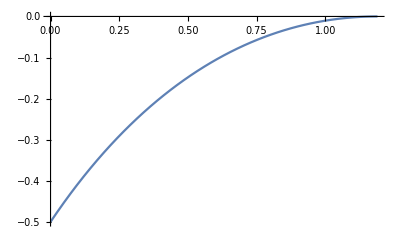

```mathematica
Plot[N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s],{s,0,1.19}]
```

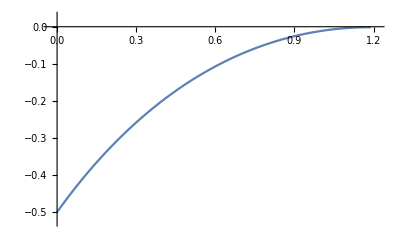

```mathematica
Abs[ NMaximize[function[s],{s}][[2]][[1]]]
```

Abs[s→-1.19061]

```mathematica
N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->10]
```

-12.4156

```mathematica
list = Table[{s,N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s]},{s,0,1.19,0.01}];
```

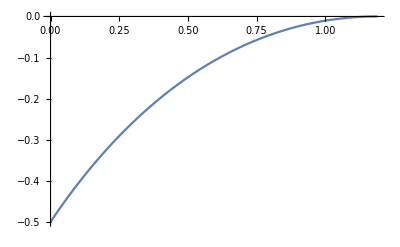

```mathematica
ListPlot[list,DataRange->{0,1.19},Joined->True]
```

```mathematica
Export["test.txt",list,"Table","FieldSeparators"->" "]
```

test.txt

```mathematica
Clear[k]
```

```mathematica
Energy[201];
```

```mathematica
function[s_] := Which[s>= 0, N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s],True, N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->-s]]
```

```mathematica
Energy[50]
```

(-50943894861009846011791822290944000000-42025478964768519415615588471467730061541933892428103680000 b^14+225785857042730761858182172987316866418550164964965816991744000 b^15-182901420680305812854696044315978618145462605859587477745958912000 b^16+32935041419358198760621764959070374287560394690524576847289647104000 b^17-102765583987227302555459377773598692045084403357635226745784238080000 b^18-43479318542947422309110042857126133375734977397756678059409158045696000 b^19-334954363291785061765479293654118048544246521159014406191082845263872000 b^20+930819219234978529921457618618038776115618624048044041703898350210508800 b^21+17431310439145525363066359711258429798130147564503138553749575075628672000 b^22+76692136388005107962483833073190473285169464302459451499458963443405036800 b^23+125065841897449419949722228004437901425516950061164891810170314778189056600 b^24-256135472530349832395697885530449873968703672450887544886793825779119234587 b^25-1231396312616485125878342033064664441044265289069422087479736452017720131584 b^26)/38928825318318844593916392505344000000

```mathematica
PartialSums[[3]]
```

-1/8+(9 b)/25-(81 b^2)/250

```mathematica
Energy[2]
```

-2/125-(81 b^2)/8

```mathematica
Clear[c,k]
```

```mathematica
Coefficients
```

{-2/(-1+k)^2,1,81/(8 k^3)-81/(8 k^2),2187/(32 k^7)-2187/(32 k^6)-2187/(32 k^5)+2187/(32 k^4),531441/(256 k^10)-177147/(64 k^9)-177147/(256 k^8)+1594323/(512 k^7)-177147/(128 k^6),-387420489/(10240 k^10)-43046721/(640 k^9)+301327047/(10240 k^8),-4261625379/(5120 k^10),0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Energy[10]
```

-(1299078 b^6+531441 b^5 c-262440 b^4 c^2+266240 c^6)/(10240 c^4)

```mathematica
Coefficients
```

{-2/(-1+k)^2,9 c,81/(8 k^3)-81/(8 k^2),243/(32 c k^7)-243/(32 c k^6)-243/(32 c k^5)+243/(32 c k^4),6561/(256 c^2 k^10)-2187/(64 c^2 k^9)-2187/(256 c^2 k^8)+19683/(512 c^2 k^7)-2187/(128 c^2 k^6),-531441/(10240 c^3 k^10)-59049/(640 c^3 k^9)+413343/(10240 c^3 k^8),-649539/(5120 c^4 k^10),0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
EnergySeries
```

-(2 (c^2 (13+12 k+11 k^2+10 k^3+9 k^4+8 k^5+7 k^6+6 k^7+5 k^8+4 k^9+3 k^10+2 k^11+k^12)))/k^10+9 c b-(81 (-1+k) b^2)/(8 k^3)+(243 (-1+k)^2 (1+k) b^3)/(32 c k^7)-(2187 (-6+8 k+2 k^2-9 k^3+4 k^4) b^4)/(512 (c^2 k^10))+(59049 (-9-16 k+7 k^2) b^5)/(10240 c^3 k^10)-(649539 b^6)/(5120 (c^4 k^10))+O[b]^21

```mathematica
Coefficients
```

{-2/(-1+k)^2,25 c,625/(8 k^3)-625/(8 k^2),15625/(96 c k^7)-15625/(96 c k^6)-15625/(96 c k^5)+15625/(96 c k^4),390625/(256 c^2 k^10)-390625/(192 c^2 k^9)-390625/(768 c^2 k^8)+1171875/(512 c^2 k^7)-390625/(384 c^2 k^6),-17578125/(2048 c^3 k^10)-1953125/(128 c^3 k^9)+13671875/(2048 c^3 k^8),-537109375/(9216 c^4 k^10),0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
c = 1/25
```

1/25

```mathematica
k=5
```

5

```mathematica
Coefficients
```

{-1/8,1,-5/2,5,-36475/1536,134375/1024,-21484375/9216,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Clear[c,k]
```